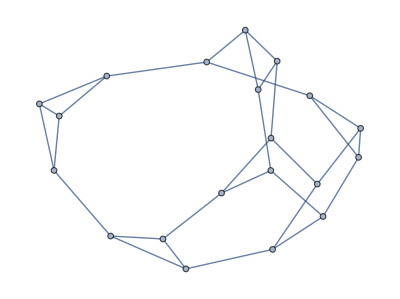

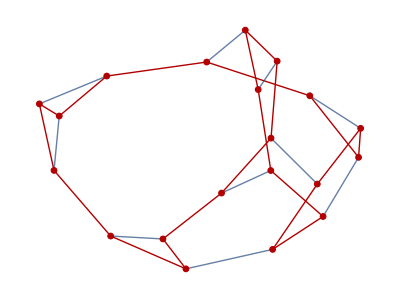

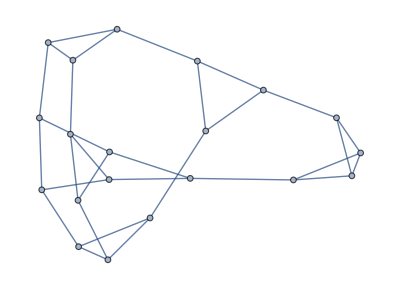

First::nofirst: {} has zero length and no first element.

-Graphics-

0

(-3+x) x (1+x) (2+x) (-2+x^2) (-3-x+x^2) (-2-2 x+2 x^2+x^3) (6+38 x+2 x^2-91 x^3-15 x^4+57 x^5+8 x^6-13 x^7-x^8+x^9)

{{1,0,0,0,0,0,0,0,0,0,1,-1,-1,0,0,0,-1,-1,1,1}}

{{1,-2,2,2,0,0,0,0,0,0,1,1,-1,-2,0,0,-1,-1,-1,1}}

√3

```mathematica
(*The Graph6 String for the two cubic graphs are "S`CGGC@?K?g?g?U??w?@??F??AP?G???k" and "S`CGGC@?G?w@G?U??w?@??C??IP?CS??o", respectively
These two graphs appeared in the paper [J.A.Filar, A. Gupta, S.K.Lucas, Connected cospectral graphs are not necessarily both Hamiltonian,  Aust.Math.Soc.Gaz.,32(2005)193].*)



n=20;
A=Table[0,{n},{n}];
L={{1,2,11,13},{2,12,14},{3,4,13,19},{4,5,14},{5,6,14},{6,7,15},{7,8,15},{8,9,15},{9,10,16},{10,11,17},{11,17},{12,17,19},{13,18},{16,18,20},{18,20},{19,20}};
For[i=1,i≤Length[L],i++,A[[L[[i]][[1]],Complement[L[[i]],{L[[i]][[1]]}]]]=Table[1,Length[L[[i]]]-1]];
A=A+Transpose[A];
G=AdjacencyGraph[A];
Print[G];
HC=FindHamiltonianCycle[G];
Print[HighlightGraph[G,PathGraph[First[HC]]]];

B=Table[0,{n},{n}];
L2={{1,2,12,20},{2,12,14},{3,4,13,19},{4,5,14},{5,6,14},{6,7,15},{7,8,15},{8,9,15},{9,10,16},{10,11,17},{11,12,18},{13,18,19},{16,18,20},{17,19,20}};
For[i=1,i≤Length[L2],i++,B[[L2[[i]][[1]],Complement[L2[[i]],{L2[[i]][[1]]}]]]=Table[1,Length[L2[[i]]]-1]];
B=B+Transpose[B];
H=AdjacencyGraph[B];
Print[H];
HC=FindHamiltonianCycle[H];
Print[HighlightGraph[G,PathGraph[First[HC]]]];
Print[CharacteristicPolynomial[A,x]-CharacteristicPolynomial[B,x]]; (* Check cospectrality*)
Print[Factor[CharacteristicPolynomial[A,x]]];
xi=NullSpace[A][[1]];
eta=NullSpace[B][[1]];
Print[NullSpace[A]];
Print[NullSpace[B]];
Print[Sqrt[eta.eta]/Sqrt[xi.xi]];
```

```mathematica
(*Determining the chromatic index by computing the chromatic polynomial of the line graph*)
```

```mathematica
LH=LineGraph[H];      
ChrPolyH=ChromaticPolynomial[LH,x];(*It takes tens of seconds to compute the chromatic polynomial*)
Print["The number of proper 3-edge-colorings is ",ChrPolyH/.{x->3}];
Print[Factor[ChrPolyH]];
```

The number of proper 3-edge-colorings is 0

(-3+x) (-2+x)^2 (-1+x) x (-8285534208+57090996736 x-199139192064 x^2+467397015040 x^3-826416663296 x^4+1167188833312 x^5-1362785738160 x^6+1344034280928 x^7-1135458332224 x^8+829285762872 x^9-526703348716 x^10+291908159648 x^11-141376521570 x^12+59820035846 x^13-22071881193 x^14+7076590716 x^15-1961023421 x^16+466198786 x^17-94120086 x^18+15916899 x^19-2212787 x^20+246272 x^21-21097 x^22+1306 x^23-52 x^24+x^25)